## Aufgabe 64

Graphen der Funktionen  f_n = x^2/(1 + n^2 x^2)

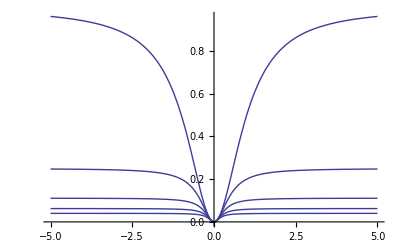

```mathematica
Plot[Table[x^2/(1+n^2x^2),{n,1,5}],{x,-5,5}]
```

Graphen der Partialsummen

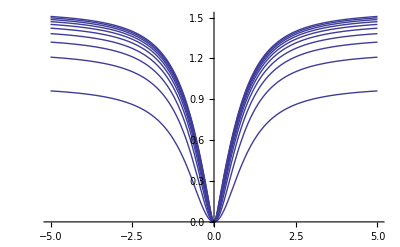

```mathematica
Plot[Table[Sum[x^2/(1+n^2x^2),{n,1,k}],{k,1,10}],{x,-5,5}]
```

## Aufgabe 65

Graphen der Funktionen f_n = (-x)^n

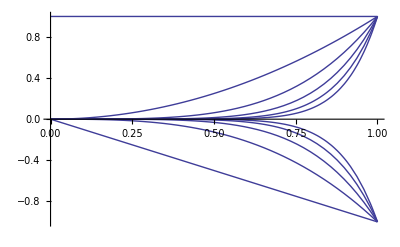

```mathematica
Plot[Table[(-1)^k*x^k,{k,0,10}],{x,0,1}]
```

Graphen der Partialsummen

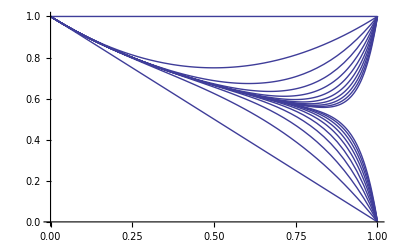

```mathematica
Plot[Table[Sum[(-1)^k*x^k,{k,0,l}],{l,0,20}],{x,0,1}]
```

Graphen der Partialsummen der integrierten Reihe

```mathematica
Table[Sum[Integrate[(-1)^k*x^k,{x,0,t}],{k,0,l}],{l,0,20}]
```

{t,t-t^2/2,t-t^2/2+t^3/3,t-t^2/2+t^3/3-t^4/4,t-t^2/2+t^3/3-t^4/4+t^5/5,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13-t^14/14,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13-t^14/14+t^15/15,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13-t^14/14+t^15/15-t^16/16,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13-t^14/14+t^15/15-t^16/16+t^17/17,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13-t^14/14+t^15/15-t^16/16+t^17/17-t^18/18,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13-t^14/14+t^15/15-t^16/16+t^17/17-t^18/18+t^19/19,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13-t^14/14+t^15/15-t^16/16+t^17/17-t^18/18+t^19/19-t^20/20,t-t^2/2+t^3/3-t^4/4+t^5/5-t^6/6+t^7/7-t^8/8+t^9/9-t^10/10+t^11/11-t^12/12+t^13/13-t^14/14+t^15/15-t^16/16+t^17/17-t^18/18+t^19/19-t^20/20+t^21/21}

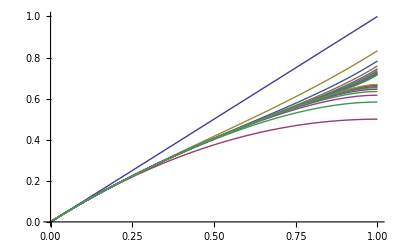

```mathematica
Plot[%,{t,0,1}]
```

Zum Vergleich : die Grenzfunktion ln (1 + x)

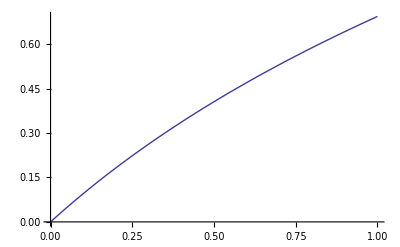

```mathematica
Plot[Log[1+x],{x,0,1}]
```